```mathematica
(*Зададим ядро уравнения*)
K[s_,t_]=Sin[t-s];
(*Проверим, является ли ядро вырожденным*)
TrigExpand[K[s,t]]
```

-Cos[t] Sin[s]+Cos[s] Sin[t]

Решение уравнения имеет вид: Cos[t]-(π^2 Cos[t])/(4 (1+π^2/4))+(π Sin[t])/(2 (1+π^2/4))

Найденная функция является решением исходного уравнения

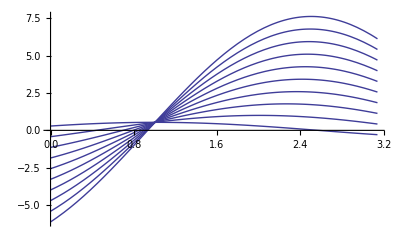

```mathematica
(*Зададим отрезок интегрирования*)
a=0;
b=Pi;
(*Зададим свободный член уравнения*)
f[t_]=Cos[t];
(*Зададим функции, входящие в вырожденное ядро уравнения*)
P={Sin[t],-Cos[t]};
Q={Cos[t],Sin[t]};
(*Найдем количество слагаемых в ядре уравнения*)
n=Dimensions[P][[1]];
(*Построим матрицу Фредгольма*)
B=Table[Integrate[Q[[k]]*P[[j]],{t,a,b}],{k,1,n},{j,1,n}];
IM=IdentityMatrix[n];
F=IM-λ*B;
(*Найдем свободные члены системы уравнений*)
A=Table[Integrate[Q[[k]]*f[t],{t,a,b}],{k,1,n}];
(*Найдем коэффициенты решения интегрального уравнения*)
c=Inverse[F].A;
(*Построим решение уравнения*)
x[t_]=f[t]+λ*Sum[c[[k]]*P[[k]],{k,1,n}];
Print["Решение уравнения имеет вид: ",x[t]]

(*Выполним проверку*)
If[FullSimplify[x[t]-λ*Integrate[K[s,t]*x[s],{s,a,b}]-f[t]]==0,
Print["Найденная функция является решением исходного уравнения"],
Print["Ищи ошибку"]
]
(*Построим графики решения данного уравнения при различных значениях параметра λ*)
G=Plot[Table[f[t]+λ*Sum[c[[k]]*P[[k]],{k,1,n}],{λ,1,10}],{t,a,b}]
```